```mathematica
p = Subscript[x, 1]^2+Subscript[x, 2]^2-1
```

-1+x_1^2+x_2^2

```mathematica
f = {{-1/2 Subscript[x, 1](Subscript[x, 1]^2+Subscript[x, 2]^2-1)}, {-1/2 Subscript[x, 2](Subscript[x, 2]^2-1)}}
```

{{-1/2 x_1 (-1+x_1^2+x_2^2)},{-1/2 x_2 (-1+x_2^2)}}

```mathematica
h = {{-Subscript[x, 2]},{Subscript[x, 1]}}
```

{{-x_2},{x_1}}

```mathematica
y = 1/2 * Subscript[x, 1]*Subscript[x, 2]
```

(x_1 x_2)/2

```mathematica
f0 = f + h * y
```

{{-1/2 x_1 x_2^2-1/2 x_1 (-1+x_1^2+x_2^2)},{1/2 x_1^2 x_2-1/2 x_2 (-1+x_2^2)}}

```mathematica
dp = ( D[p^2,{{Subscript[x, 1],Subscript[x, 2]}}].f//Expand)[[1]]
```

-2 x_1^2+4 x_1^4-2 x_1^6-2 x_2^2+6 x_1^2 x_2^2-4 x_1^4 x_2^2+4 x_2^4-4 x_1^2 x_2^4-2 x_2^6

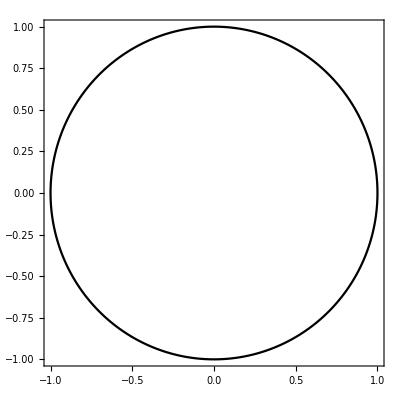

```mathematica
C1 = ContourPlot[p==0,{Subscript[x, 1],-1,1},{Subscript[x, 2],-1,1},ContourStyle-> Black,PlotPoints->100,MaxRecursion->2]
```

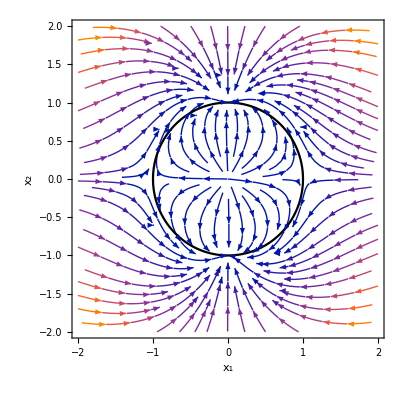

```mathematica
S1 = Show[StreamPlot[(f0 + h  * 0)[[;;, 1]],{Subscript[x, 1],-2,2},{Subscript[x, 2],-2,2}], C1,FrameLabel-> {Subscript[x, 1],Subscript[x, 2]}]
```

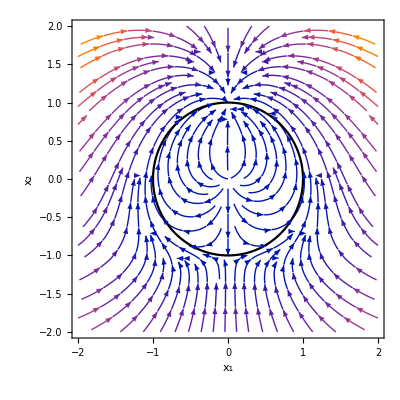

```mathematica
S2 = Show[StreamPlot[(f0 + h  * (Subscript[x, 1]))[[;;, 1]],{Subscript[x, 1],-2,2},{Subscript[x, 2],-2,2}], C1,FrameLabel-> {Subscript[x, 1],Subscript[x, 2]}]
```

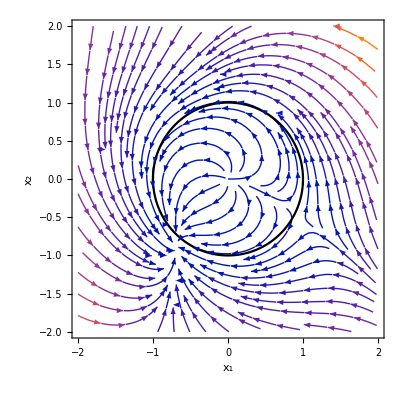

```mathematica
S3 = Show[StreamPlot[(f0 + h  * (Subscript[x, 1]^2+Subscript[x, 2]))[[;;, 1]],{Subscript[x, 1],-2,2},{Subscript[x, 2],-2,2}], C1,FrameLabel-> {Subscript[x, 1],Subscript[x, 2]}]
```

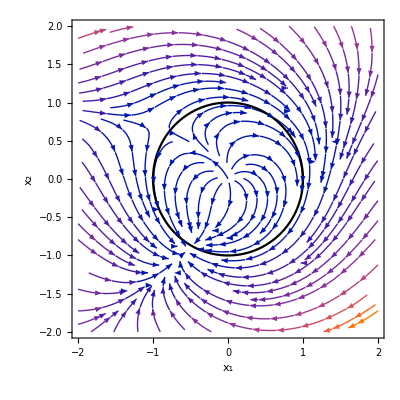

```mathematica
S4 = Show[StreamPlot[(f0 + h  * (-Subscript[x, 1]-Subscript[x, 2]^2))[[;;, 1]],{Subscript[x, 1],-2,2},{Subscript[x, 2],-2,2}], C1,FrameLabel-> {Subscript[x, 1],Subscript[x, 2]}]
```

```mathematica
Export["sp1.eps",S1]
```

sp1.eps

```mathematica
Export["sp2.eps",S2]
```

sp2.eps

```mathematica
Export["sp3.eps",S3]
```

sp3.eps

```mathematica
Export["sp4.eps",S4]
```

sp4.eps